## Slot #

```mathematica
Array[Plus[##] &, {2, 2}]
```

{{2,3},{3,4}}

```mathematica
Array[Plus[#1,#2] &, {2, 2}]
```

{{2,3},{3,4}}

```mathematica
Array[Plus[##,#2] &, {2, 2}]
```

{{3,5},{4,6}}

```mathematica
Array[Plus[## #2] &, {2,2}]
```

{{1,4},{2,8}}

```mathematica
Plus[{2,2} 2]
```

{4,4}

## Plotting

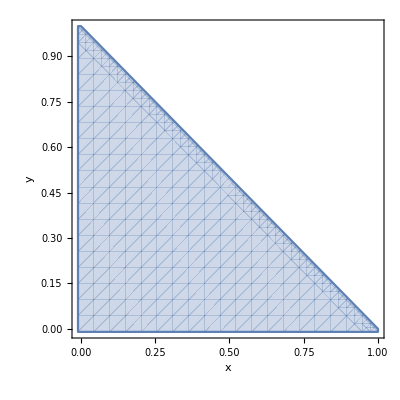

-Graphics3D-

```mathematica
RegionPlot[y<=1-x, {x,-.01,1},{y,-.01,1}, Axes:>True, AxesLabel->{x,y}]
RegionPlot3D[z<=1-x-y, {x,0,1},{y,0,1},{z,0,1}, AxesLabel->Automatic]
```

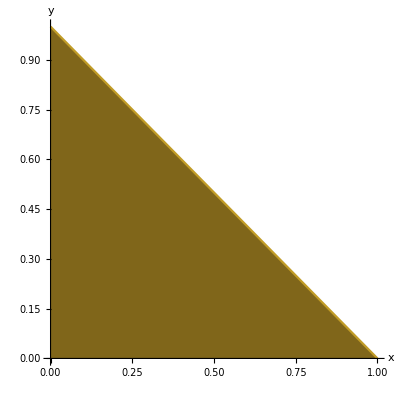

-Graphics3D-

```mathematica
Plot[1-x, {x, 0, 1}, Filling -> Bottom, AxesLabel->{x,y}, AspectRatio->Automatic] 
Plot3D[1-x-y, {x, 0, 1},{y, 0, 1}, 
RegionFunction->Function[{x,y,z}, 0<=z<=1], 
PlotStyle->Directive[Opacity[0.5,Blue]],
Filling -> Bottom, 
FillingStyle->Directive[Opacity[0.1,Blue]],
(* Mesh:>None, *) (* The mesh on the surface can be turned off *)
BoxRatios:>{1,1,1}, 
AxesLabel->{Subscript[x,1],Subscript[x,2],Subscript[x,3]},
BoundaryStyle->Directive[Red, Thick]]
```

## Dual basis vectors

```mathematica
vec = {r*Sin[θ]*Cos[ϕ], r*Sin[θ]*Sin[ϕ], r*Cos[θ] }
rmag = Simplify[Norm[vec], Assumptions->{r>0,θ∈Reals,ϕ∈Reals}]
```

{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ]}

r

```mathematica
pars = {{r, Sqrt[x^2+y^2+z^2]},
		{θ, ArcCos[z/Sqrt[x^2+y^2+z^2]]},
		{ϕ, ArcTan[y/x]}
		}
coords = {
x:> r*Sin[θ]*Cos[ϕ],
y:> r*Sin[θ]*Sin[ϕ],
z:> r*Cos[θ]
}
```

{{r,√(x^2+y^2+z^2)},{θ,ArcCos[z/(√(x^2+y^2+z^2))]},{ϕ,ArcTan[y/x]}}

{x:>r Sin[θ] Cos[ϕ],y:>r Sin[θ] Sin[ϕ],z:>r Cos[θ]}

```mathematica
e[x_] := D[vec, pars[[x,1]] ]
Do[Print[Subscript[Style[e,Bold], pars[[i,1]]], " = ", e[i]], {i,1,3}]
```

e_r = {Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

e_θ = {r Cos[θ] Cos[ϕ],r Cos[θ] Sin[ϕ],-r Sin[θ]}

e_ϕ = {-r Sin[θ] Sin[ϕ],r Cos[ϕ] Sin[θ],0}

```mathematica
g = Table[e[i].e[j], {i, 3}, {j, 3}] // Simplify ;
g // MatrixForm
```

(1 | 0 | 0
0 | r^2 | 0
0 | 0 | r^2 Sin[θ]^2)

```mathematica
f[a_] := Simplify[∇_{x,y,z} pars[[a,2]] /. coords,
				  Assumptions->{r>0,0<θ<Pi,ϕ∈Reals}
				  ] 
Do[Print[Style[e,Bold]^pars[[i,1]]," = ",f[i]], {i,1,3}]
```

e^r = {Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

e^θ = {(Cos[θ] Cos[ϕ])/r,(Cos[θ] Sin[ϕ])/r,-Sin[θ]/r}

e^ϕ = {-(Csc[θ] Sin[ϕ])/r,(Cos[ϕ] Csc[θ])/r,0}

```mathematica
check[i_] := Sum[ g[[i,j]]*f[j], {j,1,Length[g]} ] (* contract g_ij * e^j *)
Do[ Print[Subscript["e", pars[[i,1]]],(" = e")^pars[[i,1]]," ---> " ,check[i]===e[i]], {i,1,Length[g]} ]
```

e_r(= e)^r ---> True

e_θ(= e)^θ ---> True

e_ϕ(= e)^ϕ ---> True

## Tree form

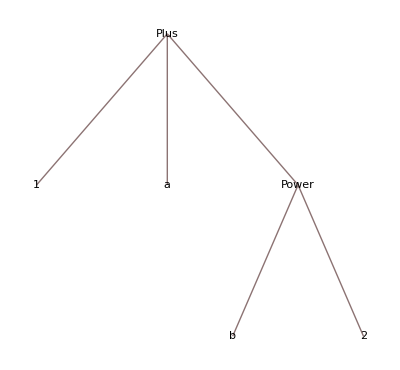

```mathematica
TreeForm[1+a+b^2]
```

SetDelayed::write: Tag List in {{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}}[a_] is Protected.

$Failed

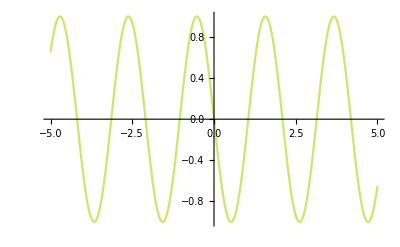

```mathematica
f[a_] := Sin[a(2*Pi-x)] 
g[a_] := Sin[-a*x]
Plot[{f[3], g[3]}, {x,-5,5}]
```

## Sound

```mathematica
EmitSound[Sound[SoundNote[{"Snare", "BassDrum"}]]]
Pause[0.08]
EmitSound[Sound[SoundNote["Snare"]]]
Pause[0.4]
Do[{EmitSound[Sound[SoundNote[{"RideCymbal", "Snare", "BassDrum2"}]]], 
Pause[0.04],
EmitSound[Sound[SoundNote["BassDrum"]]]
}, {20}]
Pause[1/2]
EmitSound[Sound[SoundNote[{"CrashCymbal", "BassDrum2"}]]]
```

## Inverting a system

```mathematica
SetDirectory[NotebookDirectory[]]
<< "result.txt";
data = %[[1,2,1;;3]]
```

/home/jkrys/gitrepos/mmaexamples

Get::noopen: Cannot open result.txt.

Part::partd: Part specification $Failed⟦1,2,1;;3⟧ is longer than depth of object.

$Failed⟦1,2,1;;3⟧

```mathematica
xs = Transpose[data][[1]]
ys = Transpose[data][[2]]
data
coeffs = NSolve[
		{a/(xs[[1]]^2) + b/xs[[1]] + c == ys[[1]], 
         a/(xs[[2]]^2) + b/xs[[2]] + c == ys[[2]],
         a/(xs[[3]]^2) + b/xs[[3]] + c == ys[[3]]
        }, 
	{a,b,c}
	];
	
Plot[a/(x^2) + b/x + c /. coeffs, {x,-0.2, 0}]
```

$Failed⟦1,2,1;;3⟧

Part::partw: Part 2 of Transpose[$Failed⟦1,2,1;;3⟧] does not exist.

Transpose[$Failed⟦1,2,1;;3⟧]⟦2⟧

$Failed⟦1,2,1;;3⟧

Part::partw: Part 3 of Transpose[$Failed⟦1,2,1;;3⟧]⟦2⟧ does not exist.

-Graphics-

## Numerical errors

```mathematica
f[x_] := 1/π Cos[80 Sin[x] - x];

res = NIntegrate[f[x], {x, 0, 2Pi}, 
  Method -> {"Trapezoidal", "SymbolicProcessing" -> 0},
  IntegrationMonitor :> ((errors = Through[#1@"Error"]) &)];

res
Length[errors]
Total[errors]

(* 
  -0.112115          <-- integral value
  2.67841*10^-15     <-- error estimate by NIntegrate
  4.996*10^-16       <-- actual error
*)
```

-0.112115

1

2.67841×10^-15

```mathematica
f[x_] := 1/π Cos[80 Sin[x] - x];

res2[a_] := NIntegrate[f[x], {x, 0, a*Pi},
 PrecisionGoal -> 7,
 IntegrationMonitor :> ((errors = Through[#1@"Error"]) &)]
res2[2]
errors;
Length[errors]
Total[errors] (* sums the errors for all subregions *)
(*
  -0.112115          <-- integral value
  175                <-- length of errors = number of subregions
  1.1067647*10^-8    <-- overall error estimate
*)
```

-0.112115

149

1.10676×10^-8

```mathematica
numvalues[{s12_,s23_}] := Module[{x,y,i},
x = ConstantArray[0, {Length[epslist], 2} ] ;
Do[x[[i]] = {epslist[[i]], res[s12,s23,epslist[[i]]]}, {i,1,Length[epslist]}];
{{s12, s23}, x}
]

num = Map[numvalues, points]
num[[1,2,1,2]]
```

points

Part::partd: Part specification points⟦1,2,1,2⟧ is longer than depth of object.

points⟦1,2,1,2⟧

```mathematica
f[x_] := 1/π Cos[80 Sin[x] - x];

iRegionMethods = {"Axis", "Boundaries", "Dimension", "Error", 
  "GetRule", "Integral", "Integrand", "WorkingPrecision"}; 
 
res = Reap@NIntegrate[f[x], {x, 0, Pi}, PrecisionGoal -> 1.1, 
   Method -> "AdaptiveMonteCarlo", 
   IntegrationMonitor :> 
    Function[{iregs}, 
     Sow[Association /@ 
       Transpose[
        Map[Thread[# -> Through[iregs[#]]] &, iRegionMethods]]]]];
Dataset[Flatten[res[[2]]]]
```

Dataset[<>]

```mathematica
numericalint00[ϵ_,s12_,s23_] :=
        (Gamma[1 - 2 ϵ] Gamma[
        2 + ϵ] (1/(-s23 x z +
        s12 y (-1 + x + y + z)))^(2 + ϵ))/(
        Gamma[1 - ϵ]^2 Gamma[1 + ϵ])

cut = 10^(-10)

numericalint[ϵ_,s12_,s23_] :=  NIntegrate[numericalint00[ϵ,s12,s23], {x,cut,1-cut}, {y,cut,1-cut-x}, {z,cut,1-cut-x-y},
MinRecursion->10^5, MaxRecursion->10^12,
Method -> {"GlobalAdaptive", "MaxErrorIncreases" ->10^4},
PrecisionGoal->4,
WorkingPrecision->20,
IntegrationMonitor :> ((errors = Through[#1@"Error"]) &)]

res = numericalint[-1/20,-3,-1]
err = Total[errors]
Print[res]
Print[err]
SetDirectory[NotebookDirectory[]]
Save["test.txt", {res,err}]
```

1/10000000000

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
numericalint00[ϵ_,s12_,s23_] :=
        (Gamma[1 - 2 ϵ] Gamma[
        2 + ϵ] (1/(-s23 x z +
        s12 y (-1 + x + y + z)))^(2 + ϵ))/(
        Gamma[1 - ϵ]^2 Gamma[1 + ϵ])

cut = 10^(-100)

numericalint[ϵ_,s12_,s23_] :=  NIntegrate[numericalint00[ϵ,s12,s23], {x,cut,1-cut}, {y,cut,1-cut-x}, {z,cut,1-cut-x-y},
MinRecursion->10^5, MaxRecursion->10^12,
Method -> {"GlobalAdaptive", "MaxErrorIncreases" ->10^7, "SingularityHandler" -> "DuffyCoordinates"},
PrecisionGoal->4,
WorkingPrecision->200,
IntegrationMonitor :> ((errors = Through[#1@"Error"]) &)]

SetDirectory[NotebookDirectory[]]
res = numericalint[-1/10,-3/2,-3/2]
err = Total[errors]
Print[res]
Print[err]

Save["test.txt", {res,err}]
```

## Parallel evaluation

```mathematica
ParallelEvaluate[$ProcessID]
ParallelEvaluate[$MachineName]
```

{49601,49602,49606,49624}

{dhcp-10-248-14-11,dhcp-10-248-14-11,dhcp-10-248-14-11,dhcp-10-248-14-11}

```mathematica
Select[Range[2000], PrimeQ[2^#-1]&] // Timing
```

{0.47384,{2,3,5,7,13,17,19,31,61,89,107,127,521,607,1279}}

```mathematica
Parallelize[Select[Range[2000], PrimeQ[2^#-1]&]] // Timing
```

{0.056637,{2,3,5,7,13,17,19,31,61,89,107,127,521,607,1279}}

```mathematica
numericalint00[ϵ_,s12_,s23_] :=
        (Gamma[1 - 2 ϵ] Gamma[
        2 + ϵ] (1/(-s23 x z +
        s12 y (-1 + x + y + z)))^(2 + ϵ))/(
        Gamma[1 - ϵ]^2 Gamma[1 + ϵ])

cut = 10^(-10);
```

```mathematica
Head[cut]
```

Rational

```mathematica
DistributeDefinitions[numericalint00,cut];
ParallelEvaluate[Head[numericalint00]]
```

{Symbol,Symbol,Symbol,Symbol}

```mathematica
ClealAll
f[x_] := 1/π Cos[80 Sin[x] - x]*Exp[-x^1.5]
test[a_] := NIntegrate[f[x], {x, 0, a*Pi}, PrecisionGoal -> 3]
Table[test[i], {i, 1, 10}] // Timing

Parallelize[Table[test[i], {i, 1, 10}]] // Timing
```

ClealAll

{0.211766,{-0.00782518,-0.00782745,-0.00782735,-0.00782745,-0.00785247,-0.00782735,-0.00782744,-0.00782745,-0.00782745,-0.00785247}}

{0.013418,{-0.00782518,-0.00782745,-0.00782735,-0.00782745,-0.00785247,-0.00782735,-0.00782744,-0.00782745,-0.00782745,-0.00785247}}

```mathematica
Table[numericalint00[i,-3,-1], {i,-0.9,0,0.2}] // Timing
Parallelize[Table[numericalint00[i,-3,-1], {i,-0.9,0,0.2}]] // Timing
```

```mathematica
numericalint[ϵ_,s12_,s23_] :=  NIntegrate[numericalint00[ϵ,s12,s23], {x,cut,1-cut}, {y,cut,1-cut-x}, {z,cut,1-cut-x-y},
MinRecursion->10^5, MaxRecursion->10^12,
Method -> {"GlobalAdaptive", "MaxErrorIncreases" ->10^4, "SingularityHandler" -> "DuffyCoordinates"},
PrecisionGoal->4,
WorkingPrecision->20,
IntegrationMonitor :> ((errors = Through[#1@"Error"]) &)]
```

```mathematica
numericalint[-1/10,-3/2,-3/2]
```

```mathematica
ParallelEvaluate[numericalint[-1/10,-3/2,-3/2]]
```

```mathematica
f[x_] := x^2
```

```mathematica
Parallelize[f[4]]
```

## Similarity Transformation

```mathematica
a = {{2,1},{-1,-1}} ;
s=Transpose[Eigenvectors[a]] ; (* Must be a transpose since the eigenvectors are given as row vectors rather than column ones *)
sinv = Inverse[s] ;
sinv.a.s // Simplify
Eigenvalues[a]
(* Eigenvalues and their order agree with the entries of the diagonalised matrix *)
```

{{1/2 (1+√5),0},{0,1/2 (1-√5)}}

{1/2 (1+√5),1/2 (1-√5)}

```mathematica
b ={{-2,5},{-1,3}} ;
t = Transpose[Eigenvectors[b]] ;
tinv = Inverse[t] ;
tinv.b.t // Simplify
Eigenvalues[b]
```

{{1/2 (1+√5),0},{0,1/2 (1-√5)}}

{1/2 (1+√5),1/2 (1-√5)}

```mathematica
p = s.tinv// Simplify
a.p - p.b (* This property is also true, see https://math.stackexchange.com/questions/625925/how-to-compute-the-similarity-transformation-matrix *)
```

{{1,-4},{0,1}}

{{0,0},{0,0}}

## Group Theory Tut 1 Q13

```mathematica
ClearAll;
u = {{a,b},{-b*, a*}} (*A matrix in the fundamental representation of SU(2) *)
ubar = u* (* Antifundamental rep *)
tprod = ArrayFlatten[u⊗ubar]  (* tensor product - Subscript[D, 2⊗Overscript[2, _]] representation*)
```

```mathematica
id = {1,0,0,1} (* The identity in 2D leaves two vectors invariant, {1,0} and {0,1}, so in the combined representation, the vector {1,0,0,1} will also be invariant *)
tprod.id /. x_*x_* :> Abs[x] /. (* Multiply id by the tensor product to check. replace aa^* = |a(|^2) *)
 Abs[a]+Abs[b] :> 1// MatrixForm (* Recall |a|^2 + |b(|^2) = 1 *)
```

```mathematica
sim = Transpose[{1/Sqrt[2]{1,0,0,1} ,1/Sqrt[2]{-1,0,0,-1},{0,1,0,0},{0,0,1,0}}];
MatrixForm[sim]
```

```mathematica
Inverse[sim].tprod.sim
```

```mathematica
sim2=Transpose[Eigenvectors[tprod]] ; (* Must be a transpose since the eigenvectors are given as row vectors rather than column ones *)
sim2inv = Inverse[sim2] ;
diag=sim2inv.tprod.sim2  //. x_*x_* :> Abs[x] /. (* Multiply id by the tensor product to check. replace aa^* = |a(|^2) *)
 Abs[a]+Abs[b] :> 1
```

## Avoid long expressions by using #

```mathematica
list = {{1,2,3},{3,4,5},{}};
(* declare the If statement as a function using &, then Map list onto the slots # *)
(* use {list} if a nested list is meant to be treated as one *) 
(* if list is not empty, return list *)
(* if list is empty, ##&[] replaces Null output with a 'vanishing function' *)
(* https://mathematica.stackexchange.com/questions/3700/how-to-avoid-returning-a-null-if-there-is-no-else-condition-in-an-if-construct *)
If[# != {}, #, ##&[]] & /@ list 
If[# != {}, #, ##&[]] & /@ {list}
```

## Save a no - argument command for later

```mathematica
dates ={};
update := AppendTo[dates,CurrentDate[]] (* needs to be := rather than = *)
update;
dates
```

{Sun 17 May 2020 02:33:53GMT+1.}

```mathematica
Do[update,{i,10}];
dates
```

{Sun 17 May 2020 02:33:53GMT+1.,Sun 17 May 2020 02:33:54GMT+1.,Sun 17 May 2020 02:33:54GMT+1.,Sun 17 May 2020 02:33:54GMT+1.,Sun 17 May 2020 02:33:54GMT+1.,Sun 17 May 2020 02:33:54GMT+1.,Sun 17 May 2020 02:33:54GMT+1.,Sun 17 May 2020 02:33:54GMT+1.,Sun 17 May 2020 02:33:54GMT+1.,Sun 17 May 2020 02:33:54GMT+1.,Sun 17 May 2020 02:33:54GMT+1.}

Perhaps with an optional argument:

```mathematica
(* https://mathematica.stackexchange.com/questions/2651/how-to-pass-a-symbol-name-to-a-function-with-any-of-the-hold-attributes/2677#2677 *)
(* https://mathematica.stackexchange.com/questions/17767/how-to-modify-function-argument *)
Clear[list]
update2[list_List] := Append[list, 6]
list={};
update2[list]
update2[%]
```

{6}

{6,6}

## NumbersBases+module+error message+grid axes labels

```mathematica
(* based on https://reference.wolfram.com/language/howto/PutHeadingsInATable.html 
			https://reference.wolfram.com/language/workflow/SetUpErrorCheckingAndMessagesInAFunction.html *)

Clear[NumbersBases]
NumbersBases::usage = "This could be a documentation for how to use this function";
(* Create a message to be printed in case an invalid base is used *)
NumbersBases::maxbase = "Maximum base `1` is larger than the allowed value - capping at 36 <-> z";

(* x_:value indicates an optional argument with default 'value'. 
   Some arguments can be specified as optional without giving the default value as Mma has some default optoins built in 
   https://reference.wolfram.com/language/tutorial/Patterns.html#17673 *)
NumbersBases[nmin_:0, nmax_, maxbase_Integer] := Module[{bases,range,data,grid},
(* Range of bases used, change notation to hexadecimal after base 10 *)
If[maxbase≤10, bases=Range[2,maxbase],
	If[maxbase<=36, bases=Join[Range[2,10], Alphabet[][[;;maxbase-10]]],
		Message[NumbersBases::maxbase,maxbase];
		bases=Join[Range[2,10], Alphabet[]]
	  ]
];
range=nmax-nmin+1;
(* Populate the table with numbers nmin-nmax in bases 2-maxbases (possible bases are 2-36 *)
data = Table[BaseForm[i,j],{i,nmin,nmax},{j,2,Length[bases]+1}];
(* Prepend a first element to the list which contains all the horizontal headings (in this case, bases) *)
data = Prepend[data,bases];
(* Prepend another `list` with one element only - the name of the heading.
   Can ensure correct placement by prepending an empty list of length equal to half of the length of the horizontal headings.
   The -1 is just to shift it nicely into the middle of the table.
   Note that Table, Range etc. can be specified with a non-integer length, e.g. Range[10.9]=Range[10.1] - like an in-built Floor function. *)
data = Prepend[data,Join[Table["",Length[bases]/2-1],{"\nBase"}]];
(* Prepend the number to the each row (apart from the first two which are just the header 'Base' and a list of the bases *)
data = MapThread[Prepend,{data,Join[{"",""},Range[nmin,nmax]]}];
(* Prepend the table title and vertical header *)
data =  MapThread[Prepend,{data,Join[{"NUMBERS/ \n BASES"},Table["", (range+2)/2],{"Numbers"},Table["",Ceiling[range/2]-1]]}];
(* Display as a grid, with frames only for the two selected rows *)
(* Elements of {{a,b},{c,d}}->True refer to: a/b = first/last rows, c/d = start/end columns *)
grid = Grid[data,{Frame->{None,None,{{{2,2},{2,-1}}->True,{{2,-1},{2,2}}->True}}}];
Return[grid];
]

?NumbersBases
NumbersBases[-2,9,39]
```

```mathematica
(* to convert from other bases to decimal, one should use base^^number *)
16^^8B54240883FA007706B800000000C383FA027706B801000000C353BB01000000B9010000008D041983FA0376078BD989
```

## Name+StringJoin+Capitalize

```mathematica
pos  = {{13,1,14,27,3}, {14,23,29,25}};
name = StringJoin /@ (Alphabet["Polish"][[#]] & /@ pos) // Capitalize (* related function: ToUpperCase/ToLowerCase *)
```

## Timing for very fast functions

```mathematica
(* If a naive attempt at timing a function returns time < $TimeUnit, then this result is not precise *)
$TimeUnit
Integrate[Sin[x],{x,-Pi,Pi}] // AbsoluteTiming
repeat = 10^3;
Do[Integrate[Sin[x],{x,-Pi,Pi}],repeat] // AbsoluteTiming 
%[[1]]/repeat (* average timing *)
(* this timing will be quicker than the original computation above, because the Kernel stores some 
   variables internally during repeatead evaluation for further use, so the subsequent computations are quicker *)
```

## Assign a value if symbol not already defined

```mathematica
ClearAll[condassign];
condassign[var_Symbol,value_:{1,2}]:=(var=value)
condassign[var_,value_:2020]:=var

Clear[a];                 
condassign[a]             (* Out: {1,2} because a had no value *)
condassign[a]             (* Out: {1,2} because a now has a value *)
b := Integrate[Sin[x],x]   (* Out: -Cos[x] because b had an assigned value *)
condassign[b]
```

{1,2}

{1,2}

-Cos[x]

## {{x1,x2}, {y1,y2}} --> {{x1,y1},{x2,y2}}

```mathematica
xvals = {a,b,c};
yvals = {d,e,f};
Riffle[xvals,yvals]
Partition[%,2]
```

{a,d,b,e,c,f}

{{a,d},{b,e},{c,f}}

## MaTeX

```mathematica
(* http://szhorvat.net/pelican/latex-typesetting-in-mathematica.html *)
(* https://github.com/szhorvat/MaTeX *)
(* Help->Wolfram Documentation->"MaTeX" *)
```

```mathematica
ResourceFunction["MaTeXInstall"][] (* install MaTeX *)
```

```mathematica
<<MaTeX`
ConfigureMaTeX[]
SetOptions[MaTeX, Magnification->1.2] (* default axis labels too small *)
```

```mathematica
"\\sum_{k=1}^\\infty \\frac{1}{k^2}" // MaTeX (* "" will take the content as literal TeX input - need \\ to escape \sin etc. *)
Sum[1/k^2,{k,1,Infinity}] // MaTeX            (* convert a Mathematica expression to TeX input *)
HoldForm[Sum[1/k^2,{k,1,Infinity}]] // MaTeX  (* need to use HoldForm to prevent Mathematica from evaluating the expression *)
MaTeX[Sin[a*x^2]]
MaTeX["\\sin(ax^2)"]                          (* the spacing is different *)
```

```mathematica
texStyle = {FontFamily -> "Latin Modern Roman", FontSize -> 12}; (* use the LaTeX font *)

ContourPlot[x^2 + y^4 == 1, {x, -1.2, 1.2}, {y, -1.2, 1.2},
 BaseStyle -> texStyle,
 Epilog -> {
     Arrow[{{0.1, 0.3}, {0.5, 0.80}}],
     Inset[MaTeX["x^2+y^4=1", Magnification -> 2], {0.1, 0.3}, Scaled[{0.5, 1}]] (* can also specify Magnification locally *)
    }]
    
Plot[Sin[x], {x, 0, 2 Pi},
 Frame -> True, FrameStyle -> BlackFrame,
 FrameTicks -> {{Automatic, None},
                {Table[{x, MaTeX[x, "DisplayStyle" -> False]}, {x, Pi/4 Range[0, 8]}], None}},
 FrameLabel -> MaTeX /@ {"x", "\\sin x"}, (* \\ needed to escape \ *)
 BaseStyle -> texStyle]
```

```mathematica
(* MaTeX only supports the kind of TeX input that would be valid in the $...$ environment, i.e. inline. *)
MaTeX["
 \\begin{equation}
 x^2
 \\end{equation}
"]
(* However, "aligned" works: *)
MaTeX["
 \\begin{aligned}
 x+y&=z \\\\
 u+v&=w
 \\end{aligned}
"]
```

## FiniteFlow

### FFAlgMul

```mathematica
<<FiniteFlow`
```

```mathematica
FFNewGraph[testgraph, input, {a,b,c}];
FFAlgRatFunEval[testgraph, vec1, {input}, {a,b,c}, {a,b,c}];
FFAlgRatFunEval[testgraph, vec2, {input}, {a,b,c}, {1,2,3}];

FFAlgMatMul[testgraph, matmul, {vec1, vec2}, 3,1,3];
FFGraphOutput[testgraph,matmul];

FFReconstructFunction[testgraph, {a,b,c}]
```

{a,2 a,3 a,b,2 b,3 b,c,2 c,3 c}

### FFAlgTake

```mathematica
<< FiniteFlow`
FFNewGraph[graph, in , {x, y}];
list = Table[x^i, {i, 20}]
FFAlgRatFunEval[graph, evalNode, {in}, {x, y}, list];
allCoeffs = f[#] & /@ Range[FFNParsOut[graph, evalNode]];
selectRules = {2, 6, 7, 15};
selectedCoeffs = allCoeffs[[selectRules]];
FFAlgTake[graph, indep, {evalNode}, {allCoeffs} -> selectedCoeffs];
FFGraphOutput[graph, indep];
FFReconstructFunction[graph, {x, y}]
```

{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19,x^20}

{x^2,x^6,x^7,x^15}

```mathematica
eqs = {x + 2 y + 3 z == 0, 3 x + 4 y + 5 z == 0, 6 x + 7 y + 8 z == 0};
(*eqs = {x + 2 y + 3 z + 7 w== 4, 3 x + 4 y + 5 z +4w == 6, -19 x + 7 y + 8 z + 3w == 9, 12 x + 5 y + 8z + 11w == 0};*)
vars = Variables[eqs/.a_==b_:>a]
Solve[eqs, vars]
```

{x,y,z}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→-2 x,z→x}}

```mathematica
FFNewGraph[testgraph,input,vars];
FFAlgDenseSolver[testgraph,solve,{input},vars,eqs,vars];
FFGraphOutput[testgraph,solve];
(*FFSolverOnlyHomogeneous[testgraph,solve]*)
solverlearn = FFDenseSolverLearn[testgraph,vars]
{depvars, indepvars} = {"DepVars", "IndepVars"} /. solverlearn;
res = FFReconstructFunction[testgraph,vars]

Print["IndepEqs = ", FFSolverIndepEqs[testgraph,solve]]
Print["NIndepEqs = ", FFSolverNIndepEqs[testgraph,solve]]
Print["NParsOut = ", FFNParsOut[testgraph]]

resmat = ArrayReshape[res, {Length[depvars],Length[indepvars]+1}];
resmat // MatrixForm
Do[Print[depvars[[i]]," = ", resmat[[i,;;-2]].indepvars + resmat[[i,-1]]],{i,Length[depvars]}];
```

{DepVars→{x,y},IndepVars→{z},ZeroVars→{}}

{1,0,-2,0}

IndepEqs = {1,2}

NIndepEqs = 2

NParsOut = 4

(1 | 0
-2 | 0)

x = z

y = -2 z

## More complicated slots

```mathematica
Function[#, Select[Times@@Boole[FreeQ[#, #] &/@{Log[x],Log[x]^2}]==0]]
Map[Function[x, Select[x, Times@@Boole[FreeQ[x, #] &/@ {a,b,c}]==1]], {a,c,d}]
Function[x, Select[{a,c,d}, Times@@Boole[FreeQ[{a,c,d}, #] &/@ {a,b,c}]==1]]
```

## TensorContract

```mathematica
(* the TensorContract[tensor, {{i,j},{k,l}...}] function contracts indices at positions {i,j}, {k,l},... of tensor(ijkl...) *)
(* e.g. To contract i and j of T(ijk), where i,j=1...n, we need to use TensorContract[T, {1,2}] *)
(* which leaves a rank-1 tensor with entries T` = {T(111)+T(221)+...+T(nn1), T(112)+T(222)+...+T(nn2) ,     ...n-times...     , T(11n)+T(22n)+...+T(nnn)}*)
(* e.g. if we have T(ijk), i,j,k=1,2, and contract i and j, we will obtain a two element rank-1 tensor (a vector) with elements: *)
(* T` = {T(111)+T(221), T(112)+T(222)} *)
```

```mathematica
tensor = {{{a[1,1,1],a[1,1,2]},{a[1,2,1],a[1,2,2]}},{{a[2,1,1],a[2,1,2]},{a[2,2,1],a[2,2,2]}}};
```

```mathematica
TensorContract[tensor,{1,2}]
%=={tensor[[1,1,1]]+tensor[[2,2,1]],tensor[[1,1,2]]+tensor[[2,2,2]]}
```

{a[1,1,1]+a[2,2,1],a[1,1,2]+a[2,2,2]}

True

```mathematica
(* of course the dimensionality of each tensor level needs to be the same *)
(* e.g. this will not work, because index i has depth 2, but index j has depth 3, so we cannot contract these two indices *)
```

```mathematica
TensorContract[{{a,b,c},{c,d,e}},{{1,2}}]
```

TensorContract::ctdims: Contraction levels {1,2} have different dimensions {2,3}.

TensorContract[{{a,b,c},{c,d,e}},{{1,2}}]

```mathematica
(* we can implement the matrix determinant using the Levi-Civita tensor *)
(* take a square matrix with rows W(1)...W(n) and form the outer product with ϵ in n-dim *)
(* we get a rank-2n tensor ϵ(ijk...n)W(n+1 n+2 ... 2n) *)
(* contract it pairwise: i with n+1, j with n+2, n with 2n *)
mat = {{1,3},{4,5}};
Det[mat]
LeviCivitaTensor[2,List]⊗mat[[1]]⊗mat[[2]];
TensorContract[%,{{1,3},{2,4}}]
```

-7

-7

```mathematica
mat = {{a,b,c},{d,e,f},{g,h,j}};
Det[mat]
LeviCivitaTensor[3,List]⊗mat[[1]]⊗mat[[2]]⊗mat[[3]];
TensorContract[%,{{1,4},{2,5},{3,6}}]
```

-c e g+b f g+c d h-a f h-b d j+a e j

-c e g+b f g+c d h-a f h-b d j+a e j

#### tr5 is parity-odd

```mathematica
(*tr5 = 4*i*eps(a,b,c,d)*p1(a)*p2(b)*p3(c)*p4(d)*)
moms = Table[p[i,j],{i,4},{j,4}]
tensor = LeviCivitaTensor[4,List]⊗moms[[1]]⊗moms[[2]]⊗moms[[3]]⊗moms[[4]];
tr5 = 4*I*TensorContract[tensor,{{1,5},{2,6},{3,7},{4,8}}];
tr5parity =4*I*TensorContract[tensor/.p[i_,j_]:>-p[i,j]/;j!=1,{{1,5},{2,6},{3,7},{4,8}}]//Simplify;
tr5-(-tr5parity)//Simplify
```

{{p[1,1],p[1,2],p[1,3],p[1,4]},{p[2,1],p[2,2],p[2,3],p[2,4]},{p[3,1],p[3,2],p[3,3],p[3,4]},{p[4,1],p[4,2],p[4,3],p[4,4]}}

0

#### tr5^2 = Gram determinant

```mathematica
Vmat = moms//Transpose;
g = {{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
GramDet = Det[2*Transpose[Vmat].g.Vmat]//Simplify;
tr5^2-GramDet//Simplify
```

0